```mathematica
(*0.1.32 Задача №1*)
```

```mathematica
(*а*)
```

```mathematica
//Запишем уравнение Шредингера для квантового гармонического осциллятора
```

```mathematica
I ℏ D[Φ[x], t] =- ℏ/(2m)D[Φ[x], x,x] + x^2/2 Φ[x]
```

```mathematica
//Первое слагаемое правой части отвечает за импульсную (кинетическую) часть так как оператор "-(I ℏ)/(2  m)∂_x  - это оператор импульса", а второе - за координатную (потенциальную)часть. Для простоты будем делать обсчеты в атомной системе единиц, а в левой части после дифференцирования обозначим все появившиеся там константы за "ε"
```

```mathematica
ε Φ[x] = -1/2 D[Φ[x], x,x] + x^2/2 Φ[x]
```

```mathematica
(*б*)
```

```mathematica
//Мы знаем, что оператор "рождения" имеет вид
```

```mathematica
SuperPlus[â] = (x- I p)/(√2)= (x- I (-I D[(), x]))/(√2)= (x-D[(), x])/(√2)
```

```mathematica
(*в*)
```

```mathematica
//Найдем решение нашего уравнения в Виде гауссовской кривой: Попробуем в качетсве волновой функции взять следующую знакомую нам гауссовскую кривую
```

```mathematica
Φ[x] = ⅇ^(-x^2/2)
```

```mathematica
//Подставим в уравнение
```

```mathematica
ε ⅇ^(-x^2/2) +1/2 D[ⅇ^(-x^2/2), x,x] - x^2/2 ⅇ^(-x^2/2)==0
```

```mathematica
ⅇ^(-x^2/2) (-1+2 ε)==0
```

```mathematica
//Отсюда находим, что  "ε = 1/2"
```

```mathematica
//Теперь нам следует отнормировать эту функцию
```

```mathematica
Solve[A∫_(-∞)^∞ (ⅇ^(-x^2/2))^2 ⅆx==1,A]
```

{{A→1/(√π)}}

```mathematica
//Тогда получаем окончательный вид решения
```

```mathematica
Φ[x] = (ⅇ^(-x^2/2))/(√π)
```

```mathematica
//Это состояние основное потому, что действие минимальное - число узлов как мы увидим далее на графике минимально именно тут.
```

```mathematica
(*г*)
```

```mathematica
//Теперь начнем действовать на это решение повышающим оператором - найдем четыре первые волновые функции возбужденных состояний. Также сразу учтем нормировку - нужно поделить на "√(n!)"
```

```mathematica
zero = (ⅇ^(-x^2/2))/(√(0!)√π)
```

(ⅇ^(-x^2/2))/(√π)

```mathematica
first = FullSimplify[(x (ⅇ^(-x^2/2))/(√π)-D[((ⅇ^(-x^2/2))/(√π)), x])/(√2)]/(√(1!))
```

ⅇ^(-x^2/2) √(2/π) x

```mathematica
second =FullSimplify[ (x first-D[(first), x])/(√2)]/(√(2!))
```

(ⅇ^(-x^2/2) (-1+2 x^2))/(√(2 π))

```mathematica
third =FullSimplify[ (x second-D[(second), x])/(√2)]/(√(3!))
```

(ⅇ^(-x^2/2) x (-3+2 x^2))/(√(6 π))

```mathematica
fourth =FullSimplify[ (x third-D[(third), x])/(√2)]/(√(4!))
```

(ⅇ^(-x^2/2) (3+4 x^2 (-3+x^2)))/(12 √(2 π))

```mathematica
//Построим их
```

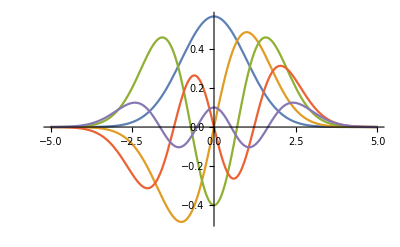

```mathematica
Plot[{zero,first ,second, third,fourth}, {x, -5,5}]
```

```mathematica
(*д*)
```

```mathematica
//Наше уравнение Шредингера является "уравнением Рикатти"
```

```mathematica
ε Φ[x] = -1/2 D[Φ[x], x,x] + x^2/2 Φ[x]
```

```mathematica
//Попробуем попросить Вольфрам решить его напрямую
```

```mathematica
DSolve[ε Φ[x] == -1/2 D[Φ[x], x,x] + x^2/2 Φ[x], Φ[x],x]
```

{{Φ[x]→C[2] ParabolicCylinderD[1/2 (-1-2 ε),ⅈ √2 x]+C[1] ParabolicCylinderD[1/2 (-1+2 ε),√2 x]}}

```mathematica
//Преобразуем это решение
```

```mathematica
FunctionExpand[{{Φ[x]->C[2] ParabolicCylinderD[1/2 (-1-2 ε),ⅈ √2 x]+C[1] ParabolicCylinderD[1/2 (-1+2 ε),√2 x]}}]
```

```mathematica
{{Φ[x]->2^(1/4 (1+2 ε)) ⅇ^(x^2/2) C[2] HermiteH[1/2 (-1-2 ε),ⅈ x]+2^(1/4 (1-2 ε)) ⅇ^(-x^2/2) C[1] HermiteH[1/2 (-1+2 ε),x]}}
```

```mathematica
//Возьмем индекс "многочлена Эрмита" и приравняем его к "n"
```

```mathematica
Solve[1/2 (-1+2 ε)==n,ε]
```

{{ε→1/2 (1+2 n)}}

```mathematica
//Это будет взаимосвязь с номером возбужденного состояния - вернем "ε" в решение, взяв например вторую ветку решения
```

```mathematica
{{Φ[x]->2^(1/4 (1-2 ε)) ⅇ^(-x^2/2) C[1] HermiteH[1/2 (-1+2 ε),x]}}/.ε->1/2 (1+2 n)
```

{{Φ[x]→2^(-n/2) ⅇ^(-x^2/2) C[1] HermiteH[n,x]}}

```mathematica
//Построим получившуюся функцию
```

```mathematica
Φ[x_,n_]:=2^(-n/2) ⅇ^(-x^2/2)  HermiteH[n,x]
```

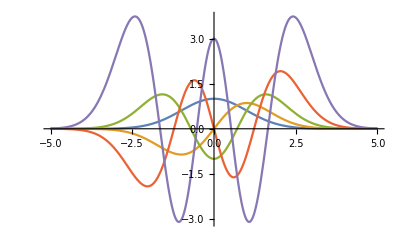

```mathematica
Plot[{Φ[x,0],Φ[x,1] ,Φ[x,2], Φ[x,3],Φ[x,4]}, {x, -5,5}]
```

```mathematica
//Видим, что это те же самые решения, только неотнормированные
```

```mathematica
(*е*)
```

```mathematica
//Теперь попробуем решить наше уравнение методом "WKB" - для начала перепишем его
```

```mathematica
ε Φ[x] = -1/2 D[Φ[x], x,x] + x^2/2 Φ[x]
```

```mathematica
//Представим нашу волновую функцию как экспоненту от действия
```

```mathematica
Φ[x_]:= Exp[I S[x]]
```

```mathematica
//Подставим это решение в функцию
```

```mathematica
ε Φ[x] +1/2 D[Φ[x], x,x] - x^2/2 Φ[x]==0
```

```mathematica
ⅇ^(ⅈ S[x]) (x^2-2 ε+S'[x]^2-ⅈ S''[x])==0
```

```mathematica
//Внутри скобок если пренебречь второй производной мы получим "уравнение Рикатти" - решим его встроенными методами
```

```mathematica
DSolve[x^2-2 ε+S'[x]^2==0,S[x],x]
```

{{S[x]→-1/2 x √(-x^2+2 ε)-ε ArcTan[x/(√(-x^2+2 ε))]+C[1]},{S[x]→1/2 x √(-x^2+2 ε)+ε ArcTan[x/(√(-x^2+2 ε))]+C[1]}}

```mathematica
//Можем решить его и руками
```

```mathematica
Solve[x^2-2 ε+S'[x]^2==0,S'[x]]
```

{{S'[x]→-√(-x^2+2 ε)},{S'[x]→√(-x^2+2 ε)}}

```mathematica
S[x] = ∫√(-x^2+2 ε)ⅆx
```

```mathematica
∫√(-x^2+2 ε)ⅆx
```

```mathematica
ΦWKB[x_,ε_] :=1/(√π)Exp[I(1/2 x √(-x^2+2 ε)+ε ArcTan[x/(√(-x^2+2 ε))])]
```

```mathematica
//Это нулевое приближение нашего решения методом WKB. Сравним графики полученные методом WKB (нормированный)и первым гауссовским решением изложенными выше
```

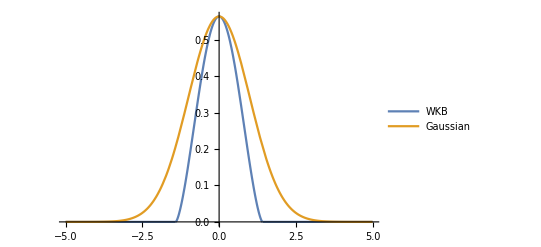

```mathematica
Plot[{Re[ΦWKB[x,1]],zero},{x, -5,5},PlotLegends->{"WKB", "Gaussian"}]
```

```mathematica
//Площади под графиками близки друг к другу, однако по графику сразу видно насколько неточен может быть "метод WKB"
```

```mathematica
(*0.1.32 Задача №2*)
```

```mathematica
//Пусть есть некоторая двууровневая система - энергия одного уровня "αt", а другого - "-αt". Эти два уровня между собой взаимодействуют
```

```mathematica
(*а*)
```

```mathematica
//Напишем уравнение Шредингера для такой системы - причем сразу будем это  делать в атомных единицах
```

```mathematica
//Для этого нам нужно записать Гамильтониан - по условию мы имеем постоянное по "x" магнитное поле и изменяющееся поле по "z", а значит, что Гамильтониан можно записать как
```

```mathematica
H = σx Hx + σz Hz
```

```mathematica
//Обезразмерим наше поле и запишем итоговое уравнение
```

```mathematica
I D[({{ψ1[t]}, {ψ2[t]}}), t] == ({{-α t, 1}, {1, α t}}).({{ψ1[t]}, {ψ2[t]}})
```

```mathematica
I D[({{ψ1[t]}, {ψ2[t]}}), t] - ({{-α t, 1}, {1, α t}}).({{ψ1[t]}, {ψ2[t]}}) ==0
```

```mathematica
(*б*)
```

```mathematica
//Перепишем  матричное уравненение в виде двух обычнх
```

```mathematica
I D[({{ψ1[t]}, {ψ2[t]}}), t] - ({{-α t, 1}, {1, α t}}).({{ψ1[t]}, {ψ2[t]}}) ==0
```

{{t α ψ1[t]-ψ2[t]+ⅈ ψ1'[t]},{-ψ1[t]-t α ψ2[t]+ⅈ ψ2'[t]}}==0

```mathematica
t α ψ1[t]-ψ2[t]+ⅈ ψ1'[t]==0
```

```mathematica
-ψ1[t]-t α ψ2[t]+ⅈ ψ2'[t]==0
```

```mathematica
//Из первого уравнения выразим "ψ2[t]" и подставим во второе
```

```mathematica
Solve[t α ψ1[t]-ψ2[t]+ⅈ ψ1'[t]==0,ψ2[t]]
```

{{ψ2[t]→t α ψ1[t]+ⅈ ψ1'[t]}}

```mathematica
-ψ1[t]-t α (t α ψ1[t]+ⅈ ψ1'[t])+ⅈ D[(t α ψ1[t]+ⅈ ψ1'[t]), t] ==0
```

```mathematica
-(1-ⅈ α+t^2 α^2) ψ1[t]-ψ1''[t]==0
```

```mathematica
//Это будет уравнение второго порядка, с которым мы и будем в основном работать
```

```mathematica
(1-ⅈ α+t^2 α^2) ψ1[t]+ψ1''[t]==0
```

```mathematica
(*в*)
```

```mathematica
//Попробуем решить это уравнение "методом WKB" - предположим, что вид волновой функции это экспонента от действия
```

```mathematica
ψ1[t_]:=ⅇ^(-I S[t])
```

```mathematica
(1-ⅈ α+t^2 α^2) ψ1[t]+ψ1''[t]==0
```

```mathematica
ⅇ^(-ⅈ S[t]) (1+α (-ⅈ+t^2 α)-S'[t]^2-ⅈ S''[t])==0
```

```mathematica
//Мы получили дифференциальное уравнение относительно действия - будем искать нулевое приближение, приравняв последний множитель к нулю
```

```mathematica
DSolve[1+α (-ⅈ+t^2 α)-S'[t]^2==0,S[t],t]
```

{{S[t]→-1/2 t √(1-ⅈ α+t^2 α^2)+C[1]-((1-ⅈ α) Log[t α+√(1-ⅈ α+t^2 α^2)])/(2 α)},{S[t]→1/2 t √(1-ⅈ α+t^2 α^2)+C[1]+((1-ⅈ α) Log[t α+√(1-ⅈ α+t^2 α^2)])/(2 α)}}

```mathematica
//Возьмем первую ветвь решения и построим её вещественную часть - фазу
```

```mathematica
Plot3D[Re[-1/2 t √(1-ⅈ α+t^2 α^2)-((1-ⅈ α) Log[t α+√(1-ⅈ α+t^2 α^2)])/(2 α)],{α,0,5},{t,-10,10}]
```

-Graphics3D-

```mathematica
//Видим неравномерное постепенно затухание. Посмотрим как это затухание происходит, построим мнимую часть
```

```mathematica
Plot3D[Im[-1/2 t √(1-ⅈ α+t^2 α^2)-((1-ⅈ α) Log[t α+√(1-ⅈ α+t^2 α^2)])/(2 α)],{α,0,5},{t,-10,10}]
```

-Graphics3D-

```mathematica
//Наше уравнение стоит заметить очень похоже на уравнение Шредингера для гармонического осциллятора
```

```mathematica
(1-ⅈ α+t^2 α^2) ψ1[t]+ψ1''[t]==0
```

```mathematica
(ε - x^2/2)Φ[x] +1/2 D[Φ[x], x,x] == 0
```

```mathematica
//Решения имеют абсолютно такую же структуру
```

```mathematica
DSolve[(1-ⅈ α+t^2 α^2) ψ[t]+ψ''[t]==0,ψ[t],t]
```

{{ψ[t]→C[2] ParabolicCylinderD[ⅈ/(2 α),(-1)^(3/4) √2 t √α]+C[1] ParabolicCylinderD[(-ⅈ-2 α)/(2 α),(-1)^(1/4) √2 t √α]}}

```mathematica
//Посмотрим на структуру решений
```

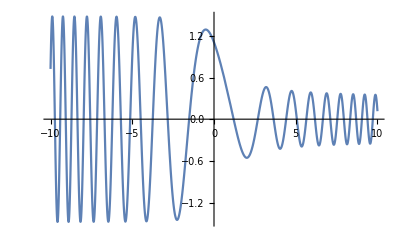

```mathematica
Plot[Re[ParabolicCylinderD[ⅈ/(2 α),(-1)^(3/4) √2 t √α]]/.{α->1},{t,-10,10}]
```

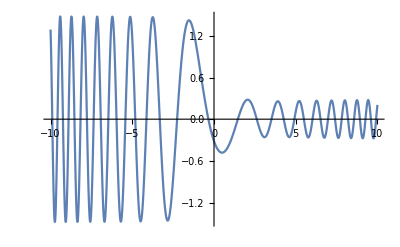

```mathematica
Plot[Im[ParabolicCylinderD[ⅈ/(2 α),(-1)^(3/4) √2 t √α]]/.{α->1},{t,-10,10}]
```

```mathematica
//Попробуем посмотреть на наше уравнение со стороны "уравнений Рикатти" - сделаем замену
```

```mathematica
Clear[ψ1]
```

```mathematica
ψ1[t]->Exp[∫y[t]ⅆt]
```

```mathematica
(1-ⅈ α+t^2 α^2)Exp[∫y[t]ⅆt]+D[(Exp[∫y[t]ⅆt]), t,t]==0
```

```mathematica
//Заметим, что уравнение полученное методом "WKB" и наше новое имеют одинаковую структуру - структуру уравнения Рикатти
```

```mathematica
ⅇ^(∫y[t]ⅆt) (1+α (-ⅈ+t^2 α)+y[t]^2+y'[t])==0
```

```mathematica
ⅇ^(-ⅈ S[t]) (1+α (-ⅈ+t^2 α)-S'[t]^2-ⅈ S''[t])==0
```

```mathematica
//Решим новое уравнение
```

```mathematica
DSolve[1+α (-ⅈ+t^2 α)+y[t]^2+y'[t]==0,y[t],t]
```

```mathematica
{{y[t]->-ⅈ t α+((1+ⅈ) √α ((1+ⅈ) t √α C[1] ParabolicCylinderD[-1-ⅈ/(2 α),(1+ⅈ) t √α]-ⅈ ParabolicCylinderD[1+ⅈ/(2 α),(-1+ⅈ) t √α]-C[1] ParabolicCylinderD[-ⅈ/(2 α),(1+ⅈ) t √α]))/(C[1] ParabolicCylinderD[-1-ⅈ/(2 α),(1+ⅈ) t √α]+ParabolicCylinderD[ⅈ/(2 α),(-1+ⅈ) t √α])}}
```

```mathematica
(*г*)
```

```mathematica
//Зная первую амплитуду, мы можем найти вторую
```

```mathematica
ψ1[t]==C[2] ParabolicCylinderD[ⅈ/(2 α),(-1)^(3/4) √2 t √α]+C[1] ParabolicCylinderD[(-ⅈ-2 α)/(2 α),(-1)^(1/4) √2 t √α]
```

```mathematica
ψ2[t]==t α (C[2] ParabolicCylinderD[ⅈ/(2 α),(-1)^(3/4) √2- t √α]+C[1] ParabolicCylinderD[(-ⅈ-2 α)/(2 α),(-1)^(1/4) √2 t √α])+ⅈ D[C[2] ParabolicCylinderD[ⅈ/(2 α),(-1)^(3/4) √2- t √α]+C[1] ParabolicCylinderD[(-ⅈ-2 α)/(2 α),(-1)^(1/4) √2 t √α],t]//FullSimplify
```

√α (2 ⅈ C[2] ParabolicCylinderD[1+ⅈ/(2 α),(-1+ⅈ)-t √α]+(2-2 ⅈ) C[1] ParabolicCylinderD[-ⅈ/(2 α),(1+ⅈ) t √α]+((1+ⅈ)+(2+ⅈ) t √α) C[2] ParabolicCylinderD[ⅈ/(2 α),(-1+ⅈ)-t √α])==2 ψ2[t]

```mathematica
//Попробуем расширить наше решение, избавившись от констант : пусть в какой-то момент времени "-Nn" наше "ψ1 == 1", a "ψ2 == 0", а также сотрем "√α"
```

```mathematica
ψ1[t]==C[2] ParabolicCylinderD[ⅈ/(2 α),(-1)^(3/4) √2 t √α]+C[1] ParabolicCylinderD[(-ⅈ-2 α)/(2 α),(-1)^(1/4) √2 t √α]
```

```mathematica
ψ2[t]==√α (2 ⅈ C[2] ParabolicCylinderD[1+ⅈ/(2 α),(-1+ⅈ)-t √α]+(2-2 ⅈ) C[1] ParabolicCylinderD[-ⅈ/(2 α),(1+ⅈ) t √α]+((1+ⅈ)+(2+ⅈ) t √α) C[2] ParabolicCylinderD[ⅈ/(2 α),(-1+ⅈ)-t √α])
```

```mathematica
ψ1[-Nn] =C[2] ParabolicCylinderD[ⅈ/(2 α),(-1)^(3/4) √2- Nn]+C[1] ParabolicCylinderD[(-ⅈ-2 α)/(2 α),(-1)^(1/4) √2 Nn]==1
```

```mathematica
ψ2[-Nn]==1/2  (2 ⅈ C[2] ParabolicCylinderD[1+ⅈ/(2 α),(-1+ⅈ)-Nn]+(2-2 ⅈ) C[1] ParabolicCylinderD[-ⅈ/(2 α),(1+ⅈ) Nn]+((1+ⅈ)+(2+ⅈ) t √α) C[2] ParabolicCylinderD[ⅈ/(2 α),(-1+ⅈ)Nn]) == 0
```

```mathematica
//Получили систему из двух уравнений на наши константы
```

```mathematica
Solve[
{C[2] ParabolicCylinderD[ⅈ/(2 α),(-1)^(3/4) √2- Nn]+C[1] ParabolicCylinderD[(-ⅈ-2 α)/(2 α),(-1)^(1/4) √2 Nn]==1,
1/2  (2 ⅈ C[2] ParabolicCylinderD[1+ⅈ/(2 α),(-1+ⅈ)-Nn]+(2-2 ⅈ) C[1] ParabolicCylinderD[-ⅈ/(2 α),(1+ⅈ) Nn]+((1+ⅈ)+(2+ⅈ) Nn) C[2] ParabolicCylinderD[ⅈ/(2 α),(-1+ⅈ)-Nn])==0},{C[1],C[2]  } ]
```

```mathematica
{{C[1]->-((ⅈ ParabolicCylinderD[1+ⅈ/(2 α),(-1+ⅈ)-Nn]+1/2 ((1+ⅈ)+(2+ⅈ) Nn) ParabolicCylinderD[ⅈ/(2 α),(-1+ⅈ)-Nn])/((1-ⅈ) ParabolicCylinderD[-ⅈ/(2 α),(1+ⅈ) Nn] ParabolicCylinderD[ⅈ/(2 α),(-1)^(3/4) √2-Nn]-(ⅈ ParabolicCylinderD[1+ⅈ/(2 α),(-1+ⅈ)-Nn]+1/2 ((1+ⅈ)+(2+ⅈ) Nn) ParabolicCylinderD[ⅈ/(2 α),(-1+ⅈ)-Nn]) ParabolicCylinderD[(-ⅈ-2 α)/(2 α),(-1)^(1/4) √2 Nn])),C[2]->((2+2 ⅈ) ParabolicCylinderD[-ⅈ/(2 α),(1+ⅈ) Nn])/((2+2 ⅈ) ParabolicCylinderD[-ⅈ/(2 α),(1+ⅈ) Nn] ParabolicCylinderD[ⅈ/(2 α),(-1)^(3/4) √2-Nn]+2 ParabolicCylinderD[1+ⅈ/(2 α),(-1+ⅈ)-Nn] ParabolicCylinderD[(-ⅈ-2 α)/(2 α),(-1)^(1/4) √2 Nn]+(1-ⅈ) ParabolicCylinderD[ⅈ/(2 α),(-1+ⅈ)-Nn] ParabolicCylinderD[(-ⅈ-2 α)/(2 α),(-1)^(1/4) √2 Nn]+(1-2 ⅈ) Nn ParabolicCylinderD[ⅈ/(2 α),(-1+ⅈ)-Nn] ParabolicCylinderD[(-ⅈ-2 α)/(2 α),(-1)^(1/4) √2 Nn])}}//FullSimplify
```

{{C[1]→(2 ParabolicCylinderD[1+ⅈ/(2 α),(-1+ⅈ)-Nn]+((1-ⅈ)+(1-2 ⅈ) Nn) ParabolicCylinderD[ⅈ/(2 α),(-1+ⅈ)-Nn])/((2+2 ⅈ) ParabolicCylinderD[-ⅈ/(2 α),(1+ⅈ) Nn] ParabolicCylinderD[ⅈ/(2 α),(-1+ⅈ)-Nn]+ParabolicCylinderD[-1-ⅈ/(2 α),(1+ⅈ) Nn] (2 ParabolicCylinderD[1+ⅈ/(2 α),(-1+ⅈ)-Nn]+((1-ⅈ)+(1-2 ⅈ) Nn) ParabolicCylinderD[ⅈ/(2 α),(-1+ⅈ)-Nn])),C[2]→((2+2 ⅈ) ParabolicCylinderD[-ⅈ/(2 α),(1+ⅈ) Nn])/((2+2 ⅈ) ParabolicCylinderD[-ⅈ/(2 α),(1+ⅈ) Nn] ParabolicCylinderD[ⅈ/(2 α),(-1+ⅈ)-Nn]+ParabolicCylinderD[-1-ⅈ/(2 α),(1+ⅈ) Nn] (2 ParabolicCylinderD[1+ⅈ/(2 α),(-1+ⅈ)-Nn]+((1-ⅈ)+(1-2 ⅈ) Nn) ParabolicCylinderD[ⅈ/(2 α),(-1+ⅈ)-Nn]))}}

```mathematica
ψ1[t_,α_,Nn_]:=(((2+2 ⅈ) ParabolicCylinderD[-ⅈ/(2 α),(1+ⅈ) Nn])/((2+2 ⅈ) ParabolicCylinderD[-ⅈ/(2 α),(1+ⅈ) Nn] ParabolicCylinderD[ⅈ/(2 α),(-1+ⅈ)-Nn]+ParabolicCylinderD[-1-ⅈ/(2 α),(1+ⅈ) Nn] (2 ParabolicCylinderD[1+ⅈ/(2 α),(-1+ⅈ)-Nn]+((1-ⅈ)+(1-2 ⅈ) Nn) ParabolicCylinderD[ⅈ/(2 α),(-1+ⅈ)-Nn])))ParabolicCylinderD[ⅈ/(2 α),(-1)^(3/4) √2 t √α]+((2 ParabolicCylinderD[1+ⅈ/(2 α),(-1+ⅈ)-Nn]+((1-ⅈ)+(1-2 ⅈ) Nn) ParabolicCylinderD[ⅈ/(2 α),(-1+ⅈ)-Nn])/((2+2 ⅈ) ParabolicCylinderD[-ⅈ/(2 α),(1+ⅈ) Nn] ParabolicCylinderD[ⅈ/(2 α),(-1+ⅈ)-Nn]+ParabolicCylinderD[-1-ⅈ/(2 α),(1+ⅈ) Nn] (2 ParabolicCylinderD[1+ⅈ/(2 α),(-1+ⅈ)-Nn]+((1-ⅈ)+(1-2 ⅈ) Nn) ParabolicCylinderD[ⅈ/(2 α),(-1+ⅈ)-Nn]))) ParabolicCylinderD[(-ⅈ-2 α)/(2 α),(-1)^(1/4) √2 t √α]
```

```mathematica
ψ2[t_,α_,Nn_]:=√α (2 ⅈ (((2+2 ⅈ) ParabolicCylinderD[-ⅈ/(2 α),(1+ⅈ) Nn])/((2+2 ⅈ) ParabolicCylinderD[-ⅈ/(2 α),(1+ⅈ) Nn] ParabolicCylinderD[ⅈ/(2 α),(-1+ⅈ)-Nn]+ParabolicCylinderD[-1-ⅈ/(2 α),(1+ⅈ) Nn] (2 ParabolicCylinderD[1+ⅈ/(2 α),(-1+ⅈ)-Nn]+((1-ⅈ)+(1-2 ⅈ) Nn) ParabolicCylinderD[ⅈ/(2 α),(-1+ⅈ)-Nn]))) ParabolicCylinderD[1+ⅈ/(2 α),(-1+ⅈ)-t √α]+(2-2 ⅈ) ((2 ParabolicCylinderD[1+ⅈ/(2 α),(-1+ⅈ)-Nn]+((1-ⅈ)+(1-2 ⅈ) Nn) ParabolicCylinderD[ⅈ/(2 α),(-1+ⅈ)-Nn])/((2+2 ⅈ) ParabolicCylinderD[-ⅈ/(2 α),(1+ⅈ) Nn] ParabolicCylinderD[ⅈ/(2 α),(-1+ⅈ)-Nn]+ParabolicCylinderD[-1-ⅈ/(2 α),(1+ⅈ) Nn] (2 ParabolicCylinderD[1+ⅈ/(2 α),(-1+ⅈ)-Nn]+((1-ⅈ)+(1-2 ⅈ) Nn) ParabolicCylinderD[ⅈ/(2 α),(-1+ⅈ)-Nn]))) ParabolicCylinderD[-ⅈ/(2 α),(1+ⅈ) t √α]+((1+ⅈ)+(2+ⅈ) t √α) (((2+2 ⅈ) ParabolicCylinderD[-ⅈ/(2 α),(1+ⅈ) Nn])/((2+2 ⅈ) ParabolicCylinderD[-ⅈ/(2 α),(1+ⅈ) Nn] ParabolicCylinderD[ⅈ/(2 α),(-1+ⅈ)-Nn]+ParabolicCylinderD[-1-ⅈ/(2 α),(1+ⅈ) Nn] (2 ParabolicCylinderD[1+ⅈ/(2 α),(-1+ⅈ)-Nn]+((1-ⅈ)+(1-2 ⅈ) Nn) ParabolicCylinderD[ⅈ/(2 α),(-1+ⅈ)-Nn]))) ParabolicCylinderD[ⅈ/(2 α),(-1+ⅈ)-t √α])
```

```mathematica
//Теперь построим амплитуды вероятности
```

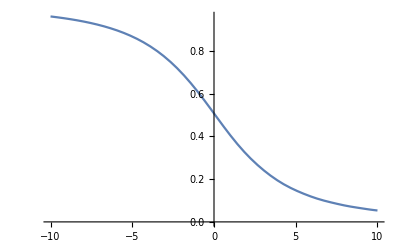

```mathematica
Plot[Abs[ψ1[t,0.2,-20]/ψ1[-20,0.2,-20]]^2,{t,-10,10}]
```

```mathematica
//Получили достаточно ровный "адиабатический" переход
```

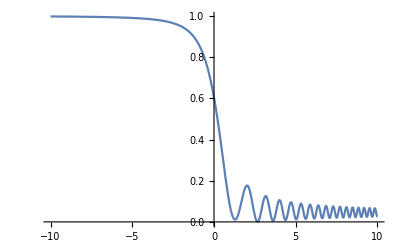

```mathematica
Plot[Abs[ψ1[t,1,-20]/ψ1[-20,1,-20]]^2,{t,-10,10}]
```

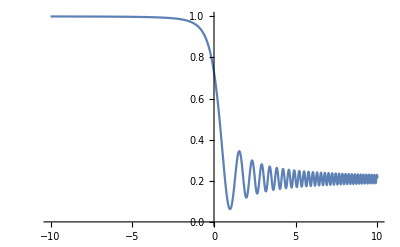

```mathematica
Plot[Abs[ψ1[t,2,-20]/ψ1[-20,2,-20]]^2,{t,-10,10}]
```

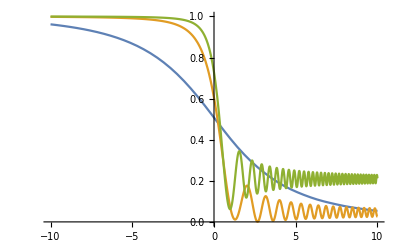

```mathematica
Plot[{(Abs[ψ1[t,0.2,-20]/ψ1[-20,0.2,-20]]^2),(Abs[ψ1[t,1,-20]/ψ1[-20,1,-20]]^2),(Abs[ψ1[t,2,-20]/ψ1[-20,2,-20]]^2)},{t,-10,10},PlotRange->{0,1}]
```

```mathematica
//Если пытаться быстро перебежать резонанс ,то появляется большая вероятность не успеть перейти на следующий уровень. Если пытаться перебежать его медленно,то больше вероятность успеха - попасть на другой уровень с минимумом рисоков. Перебежать бы не успеваем например на зеленой кривой - скорость уже слишком высока.На синей кривой мы переходим медленно,адиабатически -  уровень полностью переходит на следующий,это соотвествует неизменной заселенности равной числу "ⅇ". Оранжевая кривая-это нечто среднее.
```